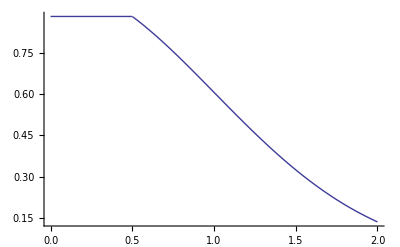

```mathematica
Gaussian[r_,σ_,amp_]:=amp*Exp[-r^2/(2*σ^2)]
modGaussian[r_,σ_,amp_,r0_]:=Piecewise[{{Gaussian[r,σ,amp],r≥r0},{Gaussian[r0,σ,amp],r<r0}}]
Plot[modGaussian[x,1,1,0.5],{x,0,2}]
```